```mathematica
n=10
```

10

```mathematica
w=25.5
l=19.6
```

25.5

19.6

```mathematica
Array[a,n]
```

{a[1],a[2],a[3],a[4],a[5],a[6],a[7],a[8],a[9],a[10]}

```mathematica
Array[a, 2n]
```

{a[1],a[2],a[3],a[4],a[5],a[6],a[7],a[8],a[9],a[10],a[11],a[12],a[13],a[14],a[15],a[16],a[17],a[18],a[19],a[20]}

```mathematica
Array[a, 2*n+1]
```

{a[1],a[2],a[3],a[4],a[5],a[6],a[7],a[8],a[9],a[10],a[11],a[12],a[13],a[14],a[15],a[16],a[17],a[18],a[19],a[20],a[21]}

```mathematica
Table[a[i]=i-1,{i,1, 2n-1}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

```mathematica
a[5]
```

4

```mathematica
For[i=0,i<2*n+1,i++,Print[i]]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

```mathematica
For[i=0,i<2*n+1,i++,Print[a[i]]]
```

a[0]

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

a[20]

```mathematica
For[i=1,i<=2*n+1,i++, a[i]=Cos[(i-1)/(2n)*Pi];Print[a[i]]]
```

1

Cos[π/20]

√(5/8+(√5)/8)

Cos[(3 π)/20]

1/4 (1+√5)

1/(√2)

√(5/8-(√5)/8)

Sin[(3 π)/20]

1/4 (-1+√5)

Sin[π/20]

0

-Sin[π/20]

1/4 (1-√5)

-Sin[(3 π)/20]

-√(5/8-(√5)/8)

-1/(√2)

1/4 (-1-√5)

-Cos[(3 π)/20]

-√(5/8+(√5)/8)

-Cos[π/20]

-1

```mathematica
For[i=1,i<=2*n+1,i++, a[i]=w/2*(1  + Cos[(i-1)/(2n)*Pi])]
```

```mathematica
Table[a[i],{i,1,2n+1}]
```

{25.5,25.343,24.876,24.1103,23.065,21.7656,20.2443,18.5384,16.69,14.7445,12.75,10.7555,8.81003,6.96162,5.25574,3.73439,2.43503,1.38967,0.624029,0.156974,0.}

```mathematica
Plot[a[i],{i,1,2n+1}]
```

-Graphics-

```mathematica
ListPlot[a[i]]
```

ListPlot::lpn: a[22.] 不是由数字或者数对组成的列表.

ListPlot[a[22]]

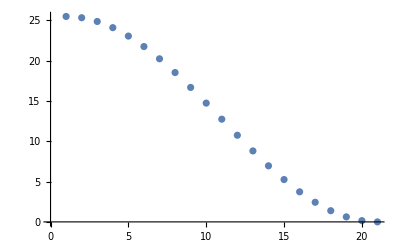

```mathematica
ListPlot[Table[{i,w/2*(1+Cos[(i-1)/(2n)*Pi])},{i,1, 2n+1,1}]]
```

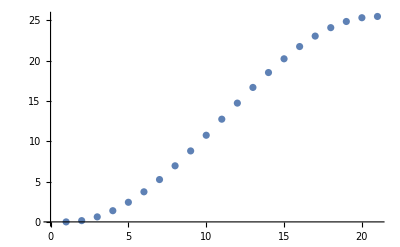

```mathematica
ListPlot[Table[{i,w/2*(1+(-1)*Cos[(i-1)/(2n)*Pi])},{i,1, 2n+1,1}]]
```

```mathematica
Array[z,2n+1]
```

{z[1],z[2],z[3],z[4],z[5],z[6],z[7],z[8],z[9],z[10],z[11],z[12],z[13],z[14],z[15],z[16],z[17],z[18],z[19],z[20],z[21]}

```mathematica
Table[z[i]=w/2*(1+(-1)*Cos[(i-1)/(2n)*Pi]),{i,1, 2n+1,1}]
```

{0.,0.156974,0.624029,1.38967,2.43503,3.73439,5.25574,6.96162,8.81003,10.7555,12.75,14.7445,16.69,18.5384,20.2443,21.7656,23.065,24.1103,24.876,25.343,25.5}

```mathematica
Array[xu,2n+1]
```

{xu[1],xu[2],xu[3],xu[4],xu[5],xu[6],xu[7],xu[8],xu[9],xu[10],xu[11],xu[12],xu[13],xu[14],xu[15],xu[16],xu[17],xu[18],xu[19],xu[20],xu[21]}

```mathematica
Array[xd,2n+1]
```

{xd[1],xd[2],xd[3],xd[4],xd[5],xd[6],xd[7],xd[8],xd[9],xd[10],xd[11],xd[12],xd[13],xd[14],xd[15],xd[16],xd[17],xd[18],xd[19],xd[20],xd[21]}

```mathematica
xu={0.1, 0.2}
```

{0.1,0.2}

```mathematica
Print[xu[3]]
```

{0.1,0.2}[3]

```mathematica
Print[xu]
```

{0.1,0.2}

```mathematica
Print[xd]
```

xd

```mathematica
xu={0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.0}
```

{0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.}

```mathematica
Print[xu]
```

{0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.}

```mathematica
Length[xu]
```

21

```mathematica
ListPlot[z,xu]
```

ListPlot::nonopt: ListPlot[z,{0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.}] 中位置 1 外应该是选项（而不是 {0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.}）. 选项必须是一个规则或者规则列表.

ListPlot[z,{0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.}]

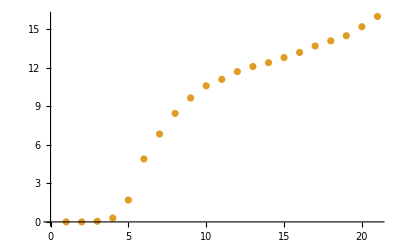

```mathematica
ListPlot[{z, xu}]
```

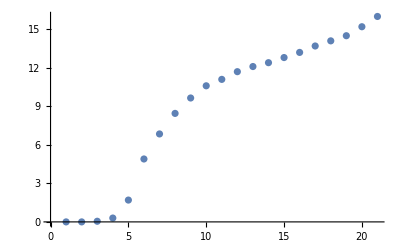

```mathematica
ListPlot[{xu,z}]
```

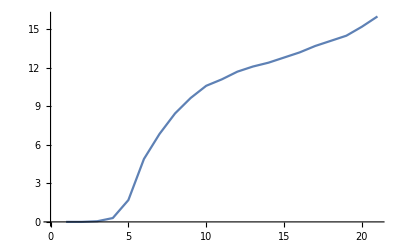

```mathematica
ListPlot[{xu,z},Joined->True]
```

```mathematica
ListPlot[{xu,z}]
```

-Graphics-

```mathematica
Options[%]
```

{DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},AxesOrigin→{0.,0},PlotRange→{{0.,21.},{0,16.}},PlotRangeClipping→True,ImagePadding→All,DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0.,0},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],Method→{CoordinatesToolOptions→{DisplayFunction→({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}},PlotRange→{{0.,21.},{0,16.}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.05]}},Ticks→{Automatic,Automatic}}

```mathematica
ListPlot[{xu,z}]
```

-Graphics-

```mathematica
show[%,AxesStyle->Arrowheads[{0,0.04}]]
```

show[-Graphics-,AxesStyle→Arrowheads[{0,0.04}]]

```mathematica
ListPlot[{xu,z}];

Show[%,AxesStyle->Arrowheads[{0,0.04}]]
```

-Graphics-

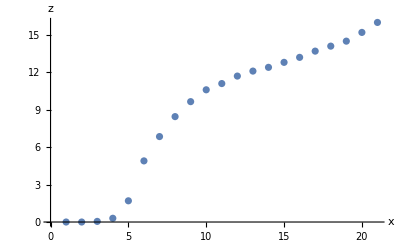

```mathematica
Show[%, AxesLabel->{x,z}]
```

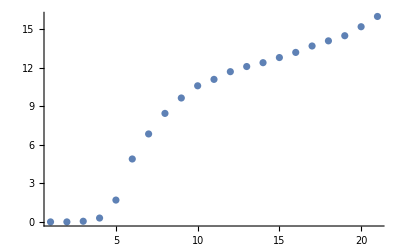

```mathematica
ListPlot[{xu,z},PlotRange->{{0,28},{17,0}}]
```

```mathematica
ListPlot[{xu,z}]
```

-Graphics-

```mathematica
ListPlot[{xd,z}]
```

-Graphics-

```mathematica
xd={19.7,19.65,19.6,19.6,19.5,19.3,19,18.3,17.3,16.6,16.5,16.8,17,17.45,17.8,18.1,18.4,18.55,18.65,18.3,17.8}
```

{19.7,19.65,19.6,19.6,19.5,19.3,19,18.3,17.3,16.6,16.5,16.8,17,17.45,17.8,18.1,18.4,18.55,18.65,18.3,17.8}

```mathematica
Length[xd]
```

21

```mathematica
%%%
```

-Graphics-

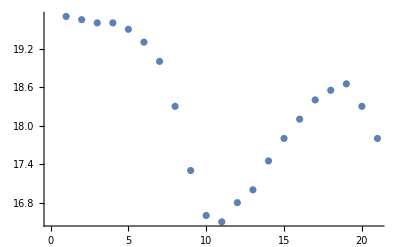

```mathematica
ListPlot[{xd,z}]
```

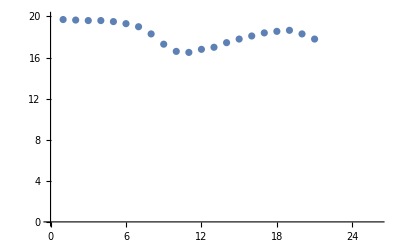

```mathematica
ListPlot[{xd,z},PlotRange->{{0,26},{0,20}}]
```

```mathematica
ListPlot[{xd,z},PlotRange->{{0,26},{0,20}}]
```

ListPlot::nonopt: ListPlot[{{19.7,19.65,19.6,19.6,19.5,19.3,19,18.3,17.3,16.6,16.5,16.8,17,17.45,17.8,18.1,18.4,18.55,18.65,18.3,17.8},z},{{0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.},z},PlotRange→{{0,26},{0,20}}] 中位置 1 外应该是选项（而不是 {{0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.},z}）. 选项必须是一个规则或者规则列表.

ListPlot[{{19.7,19.65,19.6,19.6,19.5,19.3,19,18.3,17.3,16.6,16.5,16.8,17,17.45,17.8,18.1,18.4,18.55,18.65,18.3,17.8},z},{{0,0,0.05,0.3,1.7,4.9,6.85,8.45,9.65,10.6,11.1,11.7,12.1,12.4,12.8,13.2,13.7,14.1,14.5,15.2,16.},z},PlotRange→{{0,26},{0,20}}]

```mathematica
ListPlot[{xd,z},PlotRange->{{0,26},{0,20}}]
```

-Graphics-

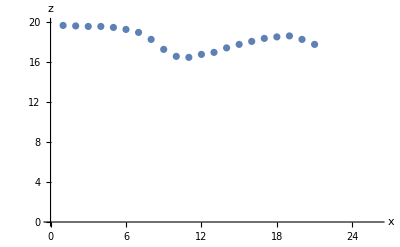

```mathematica
ListPlot[{xd,z},PlotRange->{{0,26},{0,20}},AxesLabel->{x,z}]
```

```mathematica
front=ListPlot[{xu,z}]
tail=ListPlot[{xd,z}]
```

-Graphics-

-Graphics-

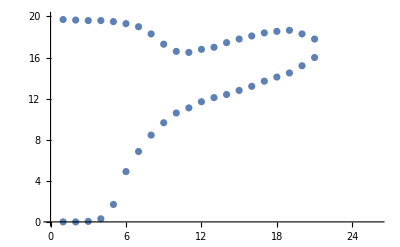

```mathematica
Show[front,tail,PlotRange->{{0,26},{0,20}}]
```